```mathematica
Quit[];
```

## Demo notebook for the ALPs EFT models

Effective field theories for a light ALP particle adopted in 1701.05379.

Contains two models:

ALP_linear - linear EFT (section 2)
ALP_chiral  - chiral EFT (section 3)

The models  only contain the ALP field and Lagrangian, so they must be loaded besides the SM.

Lagrangians defined 

LSM - SM Lagrangian
LAlp0 - Leading ALP Lagrangian. Contains ALP mass and kinetic term.
LAlp1 - Higher order terms in the ALP Lagrangian. Contains all the effective operators
LALP - LAlp0 + LAlp1

## FeynRules initialization

```mathematica
$FeynRulesPath=SetDirectory["/Users/noah/Library/Mathematica/Applications/feynrules-current"]
<<FeynRules`
SetDirectory[NotebookDirectory[]];
```

/Users/noah/Library/Mathematica/Applications/feynrules-current

- FeynRules -

Version: 2.3.43 ( 23 February 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

## ALP linear EFT

```mathematica
LoadModel["/Users/noah/Library/Mathematica/Applications/feynrules-current/Models/SM/SM.fr","/Users/noah/Library/Mathematica/Applications/feynrules-current/Models/ALP_linear_Feynrules/alp_linear.fr","/Users/noah/Library/Mathematica/Applications/feynrules-current/Models/ALP_linear_Feynrules/alp_linear_operators.fr"];
$Assumptions=cw^2+sw^2==1;
```

Merging model-files...

This model implementation was created by

I. Brivio, M.B. Gavela, L. Merlo, K. Mimasu, J.M. No, R. del Rey, V. Sanz

Model Version: 1

Please cite

arXiv:1701.05379

https://feynrules.irmp.ucl.ac.be/wiki/ALPsEFT

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model ALP_linear loaded.

### Feynman rules

```mathematica
AlpFR=FeynmanRules[LALP,MaxParticles->4]//Simplify;
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Neglecting all terms with more than 4 particles.

Collecting the different structures that enter the vertex.

3 possible non-zero vertices have been found -> starting the computation:  / 3.

3 vertices obtained.

```mathematica
decays = ComputeWidths[AlpFR]
```

Flavor expansion of the vertices:  / 3

Computing the squared matrix elements relevant for the 1->2 decays:

/ 3

Decay::Overwrite: Warning: Previous results will be overwritten.

{{{ALP,A,A},(g_aBB^2 Ma^6 (-1+s_w^2)^2)/(4 π Abs[Ma]^3)},{{ALP,A,Z},(c_w^2 g_aBB^2 (Ma^2-MZ^2)^3 s_w^2)/(2 π Abs[Ma]^3)},{{Z,A,ALP},-(c_w^2 g_aBB^2 (Ma^2-MZ^2)^3 s_w^2)/(6 π Abs[MZ]^3)},{{ALP,Z,Z},(g_aBB^2 Ma^2 (Ma^2-4 MZ^2) √(Ma^4-4 Ma^2 MZ^2) s_w^4)/(4 π Abs[Ma]^3)}}

```mathematica
decays[[1]]
decays[[2]]
decays[[4]]
```

{{ALP,A,A},(g_aBB^2 Ma^6 (-1+s_w^2)^2)/(4 π Abs[Ma]^3)}

{{ALP,A,Z},(0.12325 g_aBB^2 (Ma^2-MZ^2)^3 s_w^2)/Abs[Ma]^3}

{{ALP,Z,Z},(g_aBB^2 Ma^2 (Ma^2-4 MZ^2) √(Ma^4-4 Ma^2 MZ^2) s_w^4)/(4 π Abs[Ma]^3)}

```mathematica
?HeavisideTheta
```

```mathematica
cw = 0.88;
mz = 91.2;
```

```mathematica
TW[m_,g_]:= decayAA[m,g] + decayAZ[m,g] + decayZZ[m,g];
```

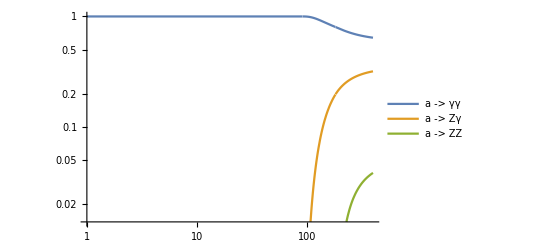

```mathematica
decayAA[m_,g_]:= g^2 m^3 cw^4/(4π);
decayAZ[m_,g_]:= g^2((m^2 - mz^2)^3)/m^3(cw^2(1 - cw^2))/(2π)HeavisideTheta[m-mz];
decayZZ[m_,g_]:= g^2((m^2 - 4 mz^2)√(m^4 - 4 m^2 mz^2)(1 - cw^2)^2)/(4π* m)HeavisideTheta[m - 2mz]
LogLogPlot[{decayAA[m,1]/TW[m,1],decayAZ[m,1]/TW[m,1],decayZZ[m,1]/TW[m,1]},{m,1,400},PlotLegends->{"a -> γγ","a -> Zγ","a -> ZZ"}]
```

```mathematica
AlpFRSimp=AlpFR//Simplify//Collect[#,{Subscript[ϵ, _]},FullSimplify]&;AlpFRSimp//TableForm
```

A | 1
A | 2
ALP | 3 | -2 ⅈ g_aBB (-1+s_w^2) ϵ_(μ_1,μ_2,mu$1,mu$2) (p_1^mu$2 p_2^mu$1-p_1^mu$1 p_2^mu$2)
A | 1
ALP | 2
Z | 3 | -2 ⅈ c_w g_aBB s_w ϵ_(μ_1,μ_3,mu$1,mu$2) (p_1^mu$2 p_3^mu$1-p_1^mu$1 p_3^mu$2)
ALP | 1
Z | 2
Z | 3 | 2 ⅈ g_aBB s_w^2 ϵ_(μ_2,μ_3,mu$1,mu$2) (p_2^mu$2 p_3^mu$1-p_2^mu$1 p_3^mu$2)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
NotebookDirectory[]
```

/Users/noahsteinberg/Desktop/ALP_notebooks/

### Export to UFO

```mathematica
WriteUFO[LSM+LALP,MaxParticles->4, Output->"ALP_linear_UFO"]
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 8 cores

Neglecting all terms with more than 4 particles.

Collecting the different structures that enter the vertex.

39 possible non-zero vertices have been found -> starting the computation:  / 39.

34 vertices obtained.

Flavor expansion of the vertices:  / 34

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 51

Squared matrix elent compute in 2.39979 seconds.

/ 61

Decay widths computed in 0.373711 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

Splitting of vertices distributed over 8 kernels.

- Optimizing: /78 .

- Writing files.

Done!

```mathematica
WriteFeynArtsOutput[LSM + LALP, CouplingRename-> False];
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Creating output directory: ALP_linear_FA

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Expanding the indices over 8 cores

Collecting the different structures that enter the vertex.

39 possible non-zero vertices have been found -> starting the computation:  / 39.

34 vertices obtained.

Writing FeynArts model file into directory ALP_linear_FA

Writing FeynArts generic file on ALP_linear_FA.gen.

```mathematica
W[Γx_,mx_,ma_]:= 1/π^2 NIntegrate[(mx*Γx)/((q1sq-mx^2)^2 + mx^2 Γx^2)*(mx*Γx)/((q2sq-mx^2)^2 + mx^2 Γx^2)decayZZ[],{q1sq,0,ma^2},{q2sq,0,(ma - √q1sq)^2}];
```

```mathematica
λ[x_,y_,z_]:= (1 - x/z - y/z)^2 - 4(x*y)/z^2;
```

```mathematica
(λ[mz^2,mz^2,ma^2])^(3/2)//FullSimplify
```

(1.-(4. mz^2)/ma^2)^(3/2)

```mathematica
Unset[mz]
```

```mathematica
Simplify[decayZZ[ma,g],Assumptions->{ma < mz && ma ∈ Reals}]
```

(0.00405012 g^2 √(ma^2-4 mz^2) (ma^2-4. mz^2) Abs[ma] HeavisideTheta[ma-2 mz])/ma